```mathematica
<<NumericalDifferentialEquationAnalysis`
<<NDSolve`FEM`
SetDirectory[NotebookDirectory[]]
Needs["MeshTools`"]
Get["/home/diogo/Dropbox/Mohr-Coulomb/mohrcoulombcrisfield2.m"]
ApplyStrainComputeSigmaDep[epst_,epsp_]:=Block[{epspr,cmat,epstint,epspint,sigprojvoigth,Dep,Dep2D,sigproj2D,sx,sy,tauxy,sz,ex,ey,exy,epse2D,G,gamma},

epstint={epst[[1]],epst[[2]],0,0,0,epst[[3]]}//N;
epspint={epsp[[1]],epsp[[2]],0,0,0,epsp[[3]]}//N;

{sigprojvoigth,Dep,cmat}=SolvePlasticity[epstint,epspint,elastmat];
(*Print["epstint = ",epstint];
Print["epspint = ",epspint];*)
epspr=Inverse[cmat].sigprojvoigth;

Dep2D={{Dep[[1,1]],Dep[[1,2]],Dep[[1,6]]},{Dep[[2,1]],Dep[[2,2]],Dep[[2,6]]},{Dep[[6,1]],Dep[[6,2]],Dep[[6,6]]}};
sigproj2D={sigprojvoigth[[1]],sigprojvoigth[[2]],sigprojvoigth[[6]]};
epse2D={epspr[[1]],epspr[[2]],epspr[[6]]};
{sigproj2D,Dep2D,epse2D}

];
FindIds[nodes_,coords_]:=Block[{nodestofind=Nearest[nodes,coords]},Flatten[Position[nodes,Alternatives@@nodestofind]]];
ComputeShape[order_,dim_]:=Block[{psis,dpsis,zeta,xi,eta },
If[dim≠1&&dim≠2 && dim≠3,Print[ "Dimension error. Need to 2D or 3D only."]; Break[];];
If[dim==1,
psis=ElementShapeFunction[LineElement,order][xi];
dpsis=Transpose[Table[{D[psis[[i]],xi],D[psis[[i]],eta]},{i,1,Length[psis]}]];
];
If[dim==2,
(*psis=ElementShapeFunction[QuadElement,order][xi,eta];
dpsis=Transpose[Table[{D[psis[[i]],xi],D[psis[[i]],eta]},{i,1,Length[psis]}]];*)
psis=ElementShapeFunction[TriangleElement,order][xi,eta];
dpsis=Transpose[Table[{D[psis[[i]],xi],D[psis[[i]],eta]},{i,1,Length[psis]}]];
];
If[dim==3,
psis=ElementShapeFunction[HexahedronElement,order][xi,eta,zeta];
dpsis=Transpose[Table[{D[psis[[i]],xi],D[psis[[i]],eta],D[psis[[i]],zeta]},{i,1,Length[psis]}]];
];
{psis,dpsis}
];


IntegrationRule[order_,dim_]:=Block[{pts,ws,npts,matpsts},
If[dim≠1&&dim≠2 && dim≠3,Print[ "Dimension error. Need to 2D or 3D only."]; Break[];];
If[dim==1,
pts=ElementIntegrationPoints[LineElement,order+1];
ws=ElementIntegrationWeights[LineElement,order+1];
matpsts=Table[{pts[[i]][[1]],0,0,ws[[i]]},{i,1,Length[ws]}];
];
If[dim==2,
(*pts=ElementIntegrationPoints[QuadElement,order+2];
ws=ElementIntegrationWeights[QuadElement,order+2];
matpsts=Table[{pts[[i]][[1]],pts[[i]][[2]],0,ws[[i]]},{i,1,Length[ws]}];*)
pts=ElementIntegrationPoints[TriangleElement,order+1];
ws=ElementIntegrationWeights[TriangleElement,order+1];
matpsts=Table[{pts[[i]][[1]],pts[[i]][[2]],0,ws[[i]]},{i,1,Length[ws]}];
];
If[dim==3,
pts=ElementIntegrationPoints[HexahedronElement,order+3];
ws=ElementIntegrationWeights[HexahedronElement,order+3];
matpsts=Table[{pts[[i]][[1]],pts[[i]][[2]],pts[[i]][[3]],ws[[i]]},{i,1,Length[ws]}];
];
matpsts
];

CalcStiff[order_,elcoords_,eldisplacement_]:=Block[{zeta,nnodes,ek,ef,intrule,psis,GradPsi,xi,eta,data,w,npts},

nnodes=Length[elcoords];
ek=Table[0,{nnodes dim},{nnodes dim}];
ef=Table[0,{nnodes dim}];
intrule=IntegrationRule[order,dim];
{psis,GradPsi}=ComputeShape[order,dim];
npts=Length[intrule];
Table[
{xi,eta,zeta,w}=intrule[[i]];
data={psis,GradPsi,elcoords,w,eldisplacement};
{ek,ef}+=Contribute[data];
,{i,1,npts}
];
{ek,ef}
];


Assemble[mesh_,displacement_]:=Block[{order,hhatv,allcoords,nodes,topol,inode,eltopology,nels,rows,sz,cols,Kglob,Fglob,co,Ke,Fe,fu,rowglob,colglob},
nodes=mesh["Coordinates"];
order=mesh["MeshOrder"];
topol=mesh["MeshElements"][[1,1]];
allcoords=Table[nodes[[topol[[i]]]],{i,1,Length[topol]}];
nels=Length[allcoords];
rows=Length[allcoords[[1]]];
sz=dim Length[nodes];
cols=rows;
Kglob=Table[0,{sz},{sz}];
Fglob=Table[0,{sz}];
uglob=Table[Table[{displacement[[dim topol[[k,j]] -1]],displacement[[dim topol[[k,j]] ]]},{j,1,Length[topol[[k]]]}],{k,1,nels}];
Table[
co=allcoords[[k]]//N;
eltopology=topol[[k]];
{Ke,Fe}=CalcStiff[order,co,uglob[[k]]];
Table[
rowglob=topol[[k,i]];
Table[
colglob=topol[[k,j]];
Table[Table[Kglob[[dim rowglob-kk,dim colglob-ll]]+=Ke[[dim i-kk,dim j-ll]],{ll,dim-1,0,-1}],{kk,dim-1,0,-1}];
,{j,1,cols}];
Table[Fglob[[dim rowglob-ll]]+=Fe[[dim i-ll]];,{ll,dim-1,0,-1}];
,{i,1,rows}];
,{k,1,nels}];
{Kglob,Fglob}
];

ContributeLineDirichlet[EK_,EF_,ids_,{dir_,val_}]:=Block[{nodes,i,j,k,Ek=EK,Ef=EF},
nodes=Length[ids];
For[i=1,i≤nodes,i++,
If[dir==1,Ek[[dim ids[[i]]-(dim-1),dim ids[[i]]-(dim-1)]]=10^12;Ef[[dim ids[[i]]-(dim-1)]]=10^12 val;];
If[dir==2,Ek[[dim ids[[i]]-(dim-2),dim ids[[i]]-(dim-2)]]=10^12;Ef[[dim ids[[i]]-(dim-2)]]=10^12 val;];
If[dir==3,Ek[[ dim ids[[i]],dim ids[[i]]]]=10^12;Ef[[dim ids[[i]] ]]=10^12 val;];
];
{Ek,Ef}
];

CoumpteStrain[gradprevsol_]:=Block[{dudx,dudy,dvdx,dvdy,gradu,strain,ex,ey,exy,ux,uy,kk},
{{dudx,dudy},{dvdx,dvdy}}=gradprevsol;
ex=dudx;
ey=dvdy;
exy=(dudy+dvdx);
{ex,ey,exy}
]

(*Compute the integration point contribution of the integral*)
Contribute[data_]:=Block[{NShapes,gamma,psis,GradPsi,Jac,x,y,nnodes,GradPhi,DetJ,InvJac,B,C,ek,ef,elcoords,weight,stress,Dep,eldisplacement,gradu,epst,epsp,epse,epspeint},
{psis,GradPsi,elcoords,weight,eldisplacement}=data;
Jac=GradPsi.elcoords;
nnodes=Length[psis];
DetJ=Det[Jac];
InvJac=Inverse[Jac];
GradPhi=InvJac.GradPsi;

If[dim==2,
B={
Flatten[Table[{GradPhi[[1,i]],0},{i,1,nnodes}],1],
Flatten[Table[{0,GradPhi[[2,i]]},{i,1,nnodes}],1],
Flatten[Table[{GradPhi[[2,i]],GradPhi[[1,i]]},{i,1,nnodes}],1]
};
NShapes={Flatten[Table[{psis[[i]],0},{i,1,Length[psis]}],1],Flatten[Table[{0,psis[[i]]},{i,1,Length[psis]}],1]};

,
B={
Flatten[Table[{GradPhi[[1,i]],0,0},{i,1,nnodes}],1],
Flatten[Table[{0,GradPhi[[2,i]],0},{i,1,nnodes}],1],
Flatten[Table[{0,0,GradPhi[[3,i]]},{i,1,nnodes}],1],
Flatten[Table[{0,GradPhi[[3,i]],GradPhi[[2,i]]},{i,1,nnodes}],1],
Flatten[Table[{GradPhi[[3,i]],0,GradPhi[[1,i]]},{i,1,nnodes}],1],
Flatten[Table[{GradPhi[[2,i]],GradPhi[[1,i]],0},{i,1,nnodes}],1]
};
NShapes={Flatten[Table[{psis[[i]],0,0},{i,1,Length[psis]}],1],Flatten[Table[{0,psis[[i]],0},{i,1,Length[psis]}],1],Flatten[Table[{0,0,psis[[i]]},{i,1,Length[psis]}],1]};
];

(*Displacement gradient*)
gradu=GradPhi.eldisplacement;
(*Infinitesimal Strain Tensor*)

epst=CoumpteStrain[gradu];

(* globalcounter =  integration point index mesh identifier. It has the size of the integration points rule multiplied by the number of mesh elements.*)
(* Plastic strain vector in the last converged step. This vector is updated when the newton method converge.  If[Converge=True, epspsolitern = epspvec] *)
epsp=epspsolitern[[globalcounter]];
(*Integration of the elastoplastic equations*)

{stress,Dep,epse}=ApplyStrainComputeSigmaDep[epst,epsp];



epspeint=epst-epse;
(*Print["epspeint = ",epspeint];*)
(*Store the plastic strain at the current integration point. When newton's method converge the values are transfered to epspsolitern=epspvec. *)
epspvec[[globalcounter]]=epspeint;
globalcounter++;
(*Element Stiffness Matrix contribution*)

ek=(Transpose[B].Dep.B)weight DetJ;

(*Element Internal force vector contribution*)
ef=(Transpose[B].stress-mult Transpose[NShapes].bodyforce)weight DetJ;

{ek,ef}
];
(*@brief Seach for topology of linear elements 
@param[in] Line ids
@param[in] polinomial order
@param[out] Line topology *)
LineTopology[ids_,order_]:=Block[{k,vg,v,j,i},
k=0;
vg={};
For[j=1,j<Length[ids]/(order),j++,
v={};
For[i=1,i≤order+1,i++,
AppendTo[v,ids[[i+k]]];
];
AppendTo[vg,v];
k+=order;
];
vg
];
(*@brief impose newmann boundary condition in a line
@param[in] nodes are mesh nodes
@param[in] polinomial order
@param[in] line ids
@param[in] normal is the direction
@param[in] f is a forcing function
@param[out] Gobal load vector *)
ContributeStraigthLineNewman[nodes_,order_,ids_,normal_,f_]:=Block[{vecint,Ef,top,i,pt,xf,x,shapes,integral,deltas,lengths},
vecint={};
Ef=Table[0,{Length[nodes]2}];
top=LineTopology[ids,order];
deltas=Table[Table[Norm[nodes[[top[[i,j]]]]-nodes[[top[[i,j+1]]]]],{j,1,order}],{i,1,Length[top]}];
If[order>1,
lengths=Table[deltas[[i,j]]+deltas[[i,j+1]],{j,1,order-1},{i,1,Length[deltas]}][[1]];
,
lengths=Flatten[deltas,1];
];
For[i=1,i≤Length[lengths],i++,
xf=lengths[[i]];
shapes=ComputeShape1D[order,x,0,xf];
integral=Table[Integrate[shapes[[i]]f[x],{x,0,xf}],{i,1,Length[shapes]}];
Table[
pt=nodes[[top[[i,j]]]];
Ef[[top[[i,j]] 2-1]]+=integral[[j]]normal[[1]];
Ef[[top[[i,j]]2]]+=integral[[j]]normal[[2]];
,
{j,1,order+1}
];
];
Ef
];
ComputeShape1D[order_,var_,x0_,xf_]:=Block[{npoints},npoints=order+1;
tab3[i_,n_]:=Table[If[j==i,1,0],{j,1,n}];
poli3[j_,n_]:=Table[{x0+(xf-x0) (i-1)/(n-1),tab3[j,n][[i]]},{i,1,n}];
ListPoli[n_]:=Table[InterpolatingPolynomial[poli3[i,n],var],{i,1,n}];
ListPoli[npoints]]
```

/home/diogo/Dropbox/Mohr-Coulomb

```mathematica
(*MAIN*)
epsttr={0.001,-0.001,0,0,0,-0.0005};
epsptr={0,0,0,0,0,0};
elastmat={20000,0.49,30 Pi/180,10};
{sig,dep,ccc}=SolvePlasticity[epsttr,epsptr,elastmat];
epsproj=Inverse[ccc].sig
epsp=epsttr-epsproj
sig//MatrixForm
dep//MatrixForm
```

{0.00095801,-0.000986572,1.6263×10^-19,0.,0.,-0.000486145}

{0.0000419903,-0.0000134282,-1.6263×10^-19,0.,0.,-0.0000138546}

(3.46631
-22.6355
-9.39288
0.
0.
-3.26272)

(6974.74 | 18624.5 | 12543.6 | 0. | 0. | 3087.58
18624.5 | 55204.5 | 36176.2 | 0. | 0. | 2941.15
12543.6 | 36176.2 | 43872.7 | 0. | 0. | 2954.08
0. | 0. | 0. | 6615.65 | 22.5519 | 0.
0. | 0. | 0. | 22.5519 | 6435.23 | 0.
3087.58 | 2941.15 | 2954.08 | 0. | 0. | 6507.14)

```mathematica
(*MAIN*)
epsttr={0,0,0,0,0,0};
epsptr={0,0,0,0,0,0};
elastmat={20000,0.49,20 Pi/180,50};
{sig,dep,ccc}=SolvePlasticity[epsttr,epsptr,elastmat];
sig//MatrixForm
dep//MatrixForm
```

(0.
0.
0.
0.
0.
0.)

(342282. | 328859. | 328859. | 0. | 0. | 0.
328859. | 342282. | 328859. | 0. | 0. | 0.
328859. | 328859. | 342282. | 0. | 0. | 0.
0. | 0. | 0. | 6711.41 | 0. | 0.
0. | 0. | 0. | 0. | 6711.41 | 0.
0. | 0. | 0. | 0. | 0. | 6711.41)

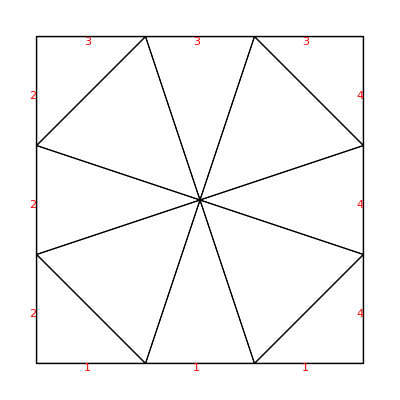

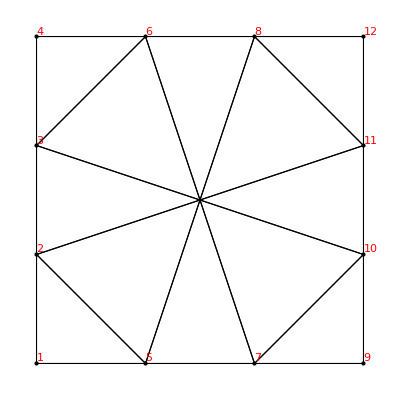

{1,5,7,9}

{4,6,8,12}

{0.,0.,0.,0.,0.,0.,0.,-0.166667,0.,0.,0.,-0.333333,0.,0.,0.,-0.333333,0.,0.,0.,0.,0.,0.,0.,-0.166667,0.,0.}

(174497. | 167785. | -3355.7 | -164430. | 0. | 0. | 0. | 0. | -171141. | -3355.7 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
167785. | 174497. | -3355.7 | -171141. | 0. | 0. | 0. | 0. | -164430. | -3355.7 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-3355.7 | -3355.7 | 229866. | 20973.2 | 23489.9 | -80536.9 | 0. | 0. | -65436.2 | 188758. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -184564. | -125839.
-164430. | -171141. | 20973.2 | 453579. | 80536.9 | -256152. | 0. | 0. | 188758. | -65436.2 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -125839. | 39149.9
0. | 0. | 23489.9 | 80536.9 | 229866. | -20973.2 | -3355.7 | 3355.7 | 0. | 0. | -65436.2 | -188758. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -184564. | 125839.
0. | 0. | -80536.9 | -256152. | -20973.2 | 453579. | 164430. | -171141. | 0. | 0. | -188758. | -65436.2 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 125839. | 39149.9
0. | 0. | 0. | 0. | -3355.7 | 164430. | 174497. | -167785. | 0. | 0. | -171141. | 3355.7 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 3355.7 | -171141. | -167785. | 174497. | 0. | 0. | 164430. | -3355.7 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-171141. | -164430. | -65436.2 | 188758. | 0. | 0. | 0. | 0. | 453579. | 20973.2 | 0. | 0. | -256152. | 80536.9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 39149.9 | -125839.
-3355.7 | -3355.7 | 188758. | -65436.2 | 0. | 0. | 0. | 0. | 20973.2 | 229866. | 0. | 0. | -80536.9 | 23489.9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -125839. | -184564.
0. | 0. | 0. | 0. | -65436.2 | -188758. | -171141. | 164430. | 0. | 0. | 453579. | -20973.2 | 0. | 0. | -256152. | -80536.9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 39149.9 | 125839.
0. | 0. | 0. | 0. | -188758. | -65436.2 | 3355.7 | -3355.7 | 0. | 0. | -20973.2 | 229866. | 0. | 0. | 80536.9 | 23489.9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 125839. | -184564.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -256152. | -80536.9 | 0. | 0. | 453579. | -20973.2 | 0. | 0. | -171141. | 164430. | -65436.2 | -188758. | 0. | 0. | 0. | 0. | 39149.9 | 125839.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 80536.9 | 23489.9 | 0. | 0. | -20973.2 | 229866. | 0. | 0. | 3355.7 | -3355.7 | -188758. | -65436.2 | 0. | 0. | 0. | 0. | 125839. | -184564.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -256152. | 80536.9 | 0. | 0. | 453579. | 20973.2 | 0. | 0. | 0. | 0. | -65436.2 | 188758. | -171141. | -164430. | 39149.9 | -125839.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -80536.9 | 23489.9 | 0. | 0. | 20973.2 | 229866. | 0. | 0. | 0. | 0. | 188758. | -65436.2 | -3355.7 | -3355.7 | -125839. | -184564.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -171141. | 3355.7 | 0. | 0. | 174497. | -167785. | -3355.7 | 164430. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 164430. | -3355.7 | 0. | 0. | -167785. | 174497. | 3355.7 | -171141. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -65436.2 | -188758. | 0. | 0. | -3355.7 | 3355.7 | 229866. | -20973.2 | 23489.9 | 80536.9 | 0. | 0. | -184564. | 125839.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -188758. | -65436.2 | 0. | 0. | 164430. | -171141. | -20973.2 | 453579. | -80536.9 | -256152. | 0. | 0. | 125839. | 39149.9
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -65436.2 | 188758. | 0. | 0. | 23489.9 | -80536.9 | 229866. | 20973.2 | -3355.7 | -3355.7 | -184564. | -125839.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 188758. | -65436.2 | 0. | 0. | 80536.9 | -256152. | 20973.2 | 453579. | -164430. | -171141. | -125839. | 39149.9
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -171141. | -3355.7 | 0. | 0. | 0. | 0. | -3355.7 | -164430. | 174497. | 167785. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -164430. | -3355.7 | 0. | 0. | 0. | 0. | -3355.7 | -171141. | 167785. | 174497. | 0. | 0.
0. | 0. | -184564. | -125839. | -184564. | 125839. | 0. | 0. | 39149.9 | -125839. | 39149.9 | 125839. | 39149.9 | 125839. | 39149.9 | -125839. | 0. | 0. | -184564. | 125839. | -184564. | -125839. | 0. | 0. | 581655. | 0.
0. | 0. | -125839. | 39149.9 | 125839. | 39149.9 | 0. | 0. | -125839. | -184564. | 125839. | -184564. | 125839. | -184564. | -125839. | -184564. | 0. | 0. | 125839. | 39149.9 | -125839. | 39149.9 | 0. | 0. | 0. | 581655.)

InterpolatingFunction[…]

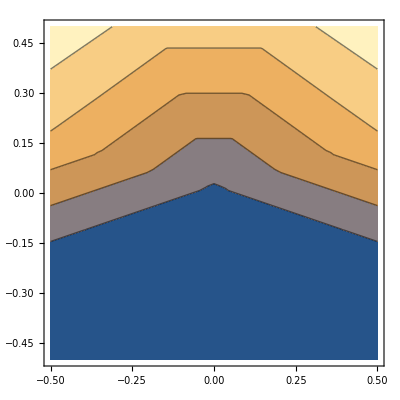

```mathematica
dim=2; (*Problem Dimension*)
order=1; (*Shape functions order*)
thick=1.;(*Thickness*)
globalcounter=1;
mult=1.;
young=20000;
nu=0.49;
elastmat={young,nu,30 Pi/180,50};
m= ToElementMesh[FullRegion[2],{{-0.5,0.5},{-0.5,0.5}},"MeshOrder"->1,MaxCellMeasure->0.2,"MeshElementType"->TriangleElement];
m=MeshOrderAlteration[m,order];
Show[m["Wireframe"],m["Wireframe"["MeshElement"->"BoundaryElements","MeshElementMarkerStyle"->Directive[Red,PointSize[0.1]]]]]
Show[m["Wireframe"],m["Wireframe"["MeshElement"->"PointElements","MeshElementIDStyle"->Red]]]
meshnodes=m["Coordinates"];
topol=m["MeshElements"][[1,1]];
intrule=IntegrationRule[order,dim];
npts=Length[intrule]; 
nglobalpts=Length[topol] npts;
epspvec=Table[0,{nglobalpts},{3}];
epspsolitern=Table[0,{nglobalpts},{3}];

x0=-0.5;
xf=0.5;
bodyforce={0,0};

coordstofind=Table[{x,-0.5},{x,-0.5,0.5,0.001}];
idsbottom=DeleteDuplicates[Flatten[Table[FindIds[meshnodes,coordstofind[[i]]],{i,1,Length[coordstofind]}]]]
coordstofind=Table[{x,0.5},{x,-0.5,0.5,0.001}];
idstop=DeleteDuplicates[Flatten[Table[FindIds[meshnodes,coordstofind[[i]]],{i,1,Length[coordstofind]}]]]

displace=Table[0,{Length[meshnodes] dim}];

f[x_]=-1;
FG=ContributeStraigthLineNewman[meshnodes,order,idstop,{0,1},f]//N
{KG,dummy}=Assemble[m,displace]//N;
KG//MatrixForm
{KG,dummy}=ContributeLineDirichlet[KG,FG,idsbottom,{1,0}];
{KG,dummy}=ContributeLineDirichlet[KG,FG,idsbottom,{2,0}];
soluu=LinearSolve[KG,FG,Method->"Banded"];
tab=Flatten[Table[Sqrt[ soluu[[i  2]]^2 +soluu[[i  2-1]]^2  ],{i, 1,Length[meshnodes] }]];
eufun=ElementMeshInterpolation[{m},tab,"ExtrapolationHandler"->{Function[Indeterminate],"WarningMessage"->False}]
ContourPlot[eufun[x,y],{x,-0.5,0.5},{y,-0.5,0.5},AspectRatio->Automatic]
```

```mathematica
f[x_]=72;
fext=ContributeStraigthLineNewman[meshnodes,order,idstop,{0,1},f];
Print["norm fext = ",Norm[fext]];
listplot={};
steps=10;
lamb=1/steps;
globalcounter=1;
tol=0.00001;
epspvec=Table[0,{nglobalpts},{3}];
epspsolitern=Table[0,{nglobalpts},{3}];
displace=Table[0,{Length[meshnodes] dim}];
print=False;
For[i=1,i<=steps,i++,
counter=1;
normres=10;
Print["step = ",i];
While[counter<10 && normres>tol,
globalcounter=1;
{stiff,fint}=Assemble[m,displace];
residual=lamb  fext-fint;
Print["displace = ",displace];
Print["norm residual = ",Norm[residual]];
Print["stiff = ",stiff//MatrixForm];

{stiff,residual}=ContributeLineDirichlet[stiff,residual,idsbottom,{1,0}];
{stiff,residual}=ContributeLineDirichlet[stiff,residual,idsbottom,{2,0}];

dws=LinearSolve[stiff,residual,Method->"Banded"];
displace+=dws;
normres=Norm[dws];
If[print==True,
Print["step = ",i, " lamb = ",lamb//N,  " iter = ",counter, " normres = ",normres];
];
counter++;
];

AppendTo[listplot,{-displace[[2 2]],lamb f[0]}];
lamb=i/steps//N;
epspsolitern=epspvec;
];
```

norm fext = 50.9117

step = 1

displace = {0,0,0,0,0,0,0,0}

norm residual = 5.09117

stiff = (174497. | 167785. | -3355.7 | -164430. | -171141. | -3355.7 | 0 | 0
167785. | 174497. | -3355.7 | -171141. | -164430. | -3355.7 | 0 | 0
-3355.7 | -3355.7 | 174497. | 0. | 0. | 167785. | -171141. | -164430.
-164430. | -171141. | 0. | 174497. | 167785. | 0. | -3355.7 | -3355.7
-171141. | -164430. | 0. | 167785. | 174497. | 0. | -3355.7 | -3355.7
-3355.7 | -3355.7 | 167785. | 0. | 0. | 174497. | -164430. | -171141.
0 | 0 | -171141. | -3355.7 | -3355.7 | -164430. | 174497. | 167785.
0 | 0 | -164430. | -3355.7 | -3355.7 | -171141. | 167785. | 174497.)

displace = {3.45949×10^-12,3.6×10^-12,5.05357×10^-6,0.0000209362,-3.45949×10^-12,3.6×10^-12,-0.000257732,0.000273615}

norm residual = 7.06089

stiff = (174497. | 167785. | -3355.7 | -164430. | -171141. | -3355.7 | 0 | 0
167785. | 174497. | -3355.7 | -171141. | -164430. | -3355.7 | 0 | 0
-3355.7 | -3355.7 | 174497. | 0. | 0. | 167785. | -171141. | -164430.
-164430. | -171141. | 0. | 174497. | 167785. | 0. | -3355.7 | -3355.7
-171141. | -164430. | 0. | 167785. | 174497. | 0. | -3355.7 | -3355.7
-3355.7 | -3355.7 | 167785. | 0. | 0. | 174497. | -164430. | -171141.
0 | 0 | -171141. | -3355.7 | -3355.7 | -164430. | 174497. | 167785.
0 | 0 | -164430. | -3355.7 | -3355.7 | -171141. | 167785. | 174497.)

step = 2

displace = {3.45949×10^-12,3.6×10^-12,5.05357×10^-6,0.0000209362,-3.45949×10^-12,3.6×10^-12,-0.000257732,0.000273615}

norm residual = 7.06089

stiff = (174497. | 167785. | -3355.7 | -164430. | -171141. | -3355.7 | 0 | 0
167785. | 174497. | -3355.7 | -171141. | -164430. | -3355.7 | 0 | 0
-3355.7 | -3355.7 | 174497. | 0. | 0. | 167785. | -171141. | -164430.
-164430. | -171141. | 0. | 174497. | 167785. | 0. | -3355.7 | -3355.7
-171141. | -164430. | 0. | 167785. | 174497. | 0. | -3355.7 | -3355.7
-3355.7 | -3355.7 | 167785. | 0. | 0. | 174497. | -164430. | -171141.
0 | 0 | -171141. | -3355.7 | -3355.7 | -164430. | 174497. | 167785.
0 | 0 | -164430. | -3355.7 | -3355.7 | -171141. | 167785. | 174497.)

step = 3

displace = {3.45949×10^-12,3.6×10^-12,5.05357×10^-6,0.0000209362,-3.45949×10^-12,3.6×10^-12,-0.000257732,0.000273615}

norm residual = 8.70495

stiff = (174497. | 167785. | -3355.7 | -164430. | -171141. | -3355.7 | 0 | 0
167785. | 174497. | -3355.7 | -171141. | -164430. | -3355.7 | 0 | 0
-3355.7 | -3355.7 | 174497. | 0. | 0. | 167785. | -171141. | -164430.
-164430. | -171141. | 0. | 174497. | 167785. | 0. | -3355.7 | -3355.7
-171141. | -164430. | 0. | 167785. | 174497. | 0. | -3355.7 | -3355.7
-3355.7 | -3355.7 | 167785. | 0. | 0. | 174497. | -164430. | -171141.
0 | 0 | -171141. | -3355.7 | -3355.7 | -164430. | 174497. | 167785.
0 | 0 | -164430. | -3355.7 | -3355.7 | -171141. | 167785. | 174497.)

displace = {6.91898×10^-12,7.2×10^-12,0.0000101071,0.0000418724,-6.91898×10^-12,7.2×10^-12,-0.000515464,0.000547229}

norm residual = 14.1218

stiff = (174497. | 167785. | -3355.7 | -164430. | -171141. | -3355.7 | 0 | 0
167785. | 174497. | -3355.7 | -171141. | -164430. | -3355.7 | 0 | 0
-3355.7 | -3355.7 | 174497. | 0. | 0. | 167785. | -171141. | -164430.
-164430. | -171141. | 0. | 174497. | 167785. | 0. | -3355.7 | -3355.7
-171141. | -164430. | 0. | 167785. | 174497. | 0. | -3355.7 | -3355.7
-3355.7 | -3355.7 | 167785. | 0. | 0. | 174497. | -164430. | -171141.
0 | 0 | -171141. | -3355.7 | -3355.7 | -164430. | 174497. | 167785.
0 | 0 | -164430. | -3355.7 | -3355.7 | -171141. | 167785. | 174497.)

step = 4

displace = {6.91898×10^-12,7.2×10^-12,0.0000101071,0.0000418724,-6.91898×10^-12,7.2×10^-12,-0.000515464,0.000547229}

norm residual = 15.0115

stiff = (174497. | 167785. | -3355.7 | -164430. | -171141. | -3355.7 | 0 | 0
167785. | 174497. | -3355.7 | -171141. | -164430. | -3355.7 | 0 | 0
-3355.7 | -3355.7 | 174497. | 0. | 0. | 167785. | -171141. | -164430.
-164430. | -171141. | 0. | 174497. | 167785. | 0. | -3355.7 | -3355.7
-171141. | -164430. | 0. | 167785. | 174497. | 0. | -3355.7 | -3355.7
-3355.7 | -3355.7 | 167785. | 0. | 0. | 174497. | -164430. | -171141.
0 | 0 | -171141. | -3355.7 | -3355.7 | -164430. | 174497. | 167785.
0 | 0 | -164430. | -3355.7 | -3355.7 | -171141. | 167785. | 174497.)

displace = {1.03785×10^-11,1.08×10^-11,0.0000151607,0.0000628086,-1.03785×10^-11,1.08×10^-11,-0.000773196,0.000820844}

norm residual = 21.1827

stiff = (174497. | 167785. | -3355.7 | -164430. | -171141. | -3355.7 | 0 | 0
167785. | 174497. | -3355.7 | -171141. | -164430. | -3355.7 | 0 | 0
-3355.7 | -3355.7 | 174497. | 0. | 0. | 167785. | -171141. | -164430.
-164430. | -171141. | 0. | 174497. | 167785. | 0. | -3355.7 | -3355.7
-171141. | -164430. | 0. | 167785. | 174497. | 0. | -3355.7 | -3355.7
-3355.7 | -3355.7 | 167785. | 0. | 0. | 174497. | -164430. | -171141.
0 | 0 | -171141. | -3355.7 | -3355.7 | -164430. | 174497. | 167785.
0 | 0 | -164430. | -3355.7 | -3355.7 | -171141. | 167785. | 174497.)

step = 5

displace = {1.03785×10^-11,1.08×10^-11,0.0000151607,0.0000628086,-1.03785×10^-11,1.08×10^-11,-0.000773196,0.000820844}

norm residual = 21.7859

stiff = (174497. | 167785. | -3355.7 | -164430. | -171141. | -3355.7 | 0 | 0
167785. | 174497. | -3355.7 | -171141. | -164430. | -3355.7 | 0 | 0
-3355.7 | -3355.7 | 174497. | 0. | 0. | 167785. | -171141. | -164430.
-164430. | -171141. | 0. | 174497. | 167785. | 0. | -3355.7 | -3355.7
-171141. | -164430. | 0. | 167785. | 174497. | 0. | -3355.7 | -3355.7
-3355.7 | -3355.7 | 167785. | 0. | 0. | 174497. | -164430. | -171141.
0 | 0 | -171141. | -3355.7 | -3355.7 | -164430. | 174497. | 167785.
0 | 0 | -164430. | -3355.7 | -3355.7 | -171141. | 167785. | 174497.)

displace = {1.3838×10^-11,1.44×10^-11,0.0000202143,0.0000837449,-1.3838×10^-11,1.44×10^-11,-0.00103093,0.00109446}

norm residual = 28.2435

stiff = (174497. | 167785. | -3355.7 | -164430. | -171141. | -3355.7 | 0 | 0
167785. | 174497. | -3355.7 | -171141. | -164430. | -3355.7 | 0 | 0
-3355.7 | -3355.7 | 174497. | 0. | 0. | 167785. | -171141. | -164430.
-164430. | -171141. | 0. | 174497. | 167785. | 0. | -3355.7 | -3355.7
-171141. | -164430. | 0. | 167785. | 174497. | 0. | -3355.7 | -3355.7
-3355.7 | -3355.7 | 167785. | 0. | 0. | 174497. | -164430. | -171141.
0 | 0 | -171141. | -3355.7 | -3355.7 | -164430. | 174497. | 167785.
0 | 0 | -164430. | -3355.7 | -3355.7 | -171141. | 167785. | 174497.)

step = 6

displace = {1.3838×10^-11,1.44×10^-11,0.0000202143,0.0000837449,-1.3838×10^-11,1.44×10^-11,-0.00103093,0.00109446}

norm residual = 28.6987

stiff = (174497. | 167785. | -3355.7 | -164430. | -171141. | -3355.7 | 0 | 0
167785. | 174497. | -3355.7 | -171141. | -164430. | -3355.7 | 0 | 0
-3355.7 | -3355.7 | 174497. | 0. | 0. | 167785. | -171141. | -164430.
-164430. | -171141. | 0. | 174497. | 167785. | 0. | -3355.7 | -3355.7
-171141. | -164430. | 0. | 167785. | 174497. | 0. | -3355.7 | -3355.7
-3355.7 | -3355.7 | 167785. | 0. | 0. | 174497. | -164430. | -171141.
0 | 0 | -171141. | -3355.7 | -3355.7 | -164430. | 174497. | 167785.
0 | 0 | -164430. | -3355.7 | -3355.7 | -171141. | 167785. | 174497.)

displace = {1.72974×10^-11,1.8×10^-11,0.0000252678,0.000104681,-1.72974×10^-11,1.8×10^-11,-0.00128866,0.00136807}

norm residual = 35.3044

stiff = (174497. | 167785. | -3355.7 | -164430. | -171141. | -3355.7 | 0 | 0
167785. | 174497. | -3355.7 | -171141. | -164430. | -3355.7 | 0 | 0
-3355.7 | -3355.7 | 174497. | 0. | 0. | 167785. | -171141. | -164430.
-164430. | -171141. | 0. | 174497. | 167785. | 0. | -3355.7 | -3355.7
-171141. | -164430. | 0. | 167785. | 174497. | 0. | -3355.7 | -3355.7
-3355.7 | -3355.7 | 167785. | 0. | 0. | 174497. | -164430. | -171141.
0 | 0 | -171141. | -3355.7 | -3355.7 | -164430. | 174497. | 167785.
0 | 0 | -164430. | -3355.7 | -3355.7 | -171141. | 167785. | 174497.)

step = 7

displace = {1.72974×10^-11,1.8×10^-11,0.0000252678,0.000104681,-1.72974×10^-11,1.8×10^-11,-0.00128866,0.00136807}

norm residual = 35.6696

stiff = (174497. | 167785. | -3355.7 | -164430. | -171141. | -3355.7 | 0 | 0
167785. | 174497. | -3355.7 | -171141. | -164430. | -3355.7 | 0 | 0
-3355.7 | -3355.7 | 174497. | 0. | 0. | 167785. | -171141. | -164430.
-164430. | -171141. | 0. | 174497. | 167785. | 0. | -3355.7 | -3355.7
-171141. | -164430. | 0. | 167785. | 174497. | 0. | -3355.7 | -3355.7
-3355.7 | -3355.7 | 167785. | 0. | 0. | 174497. | -164430. | -171141.
0 | 0 | -171141. | -3355.7 | -3355.7 | -164430. | 174497. | 167785.
0 | 0 | -164430. | -3355.7 | -3355.7 | -171141. | 167785. | 174497.)

displace = {2.07569×10^-11,2.16×10^-11,0.0000303214,0.000125617,-2.07569×10^-11,2.16×10^-11,-0.00154639,0.00164169}

norm residual = 42.3653

stiff = (174497. | 167785. | -3355.7 | -164430. | -171141. | -3355.7 | 0 | 0
167785. | 174497. | -3355.7 | -171141. | -164430. | -3355.7 | 0 | 0
-3355.7 | -3355.7 | 174497. | 0. | 0. | 167785. | -171141. | -164430.
-164430. | -171141. | 0. | 174497. | 167785. | 0. | -3355.7 | -3355.7
-171141. | -164430. | 0. | 167785. | 174497. | 0. | -3355.7 | -3355.7
-3355.7 | -3355.7 | 167785. | 0. | 0. | 174497. | -164430. | -171141.
0 | 0 | -171141. | -3355.7 | -3355.7 | -164430. | 174497. | 167785.
0 | 0 | -164430. | -3355.7 | -3355.7 | -171141. | 167785. | 174497.)

step = 8

displace = {2.07569×10^-11,2.16×10^-11,0.0000303214,0.000125617,-2.07569×10^-11,2.16×10^-11,-0.00154639,0.00164169}

norm residual = 42.6701

stiff = (174497. | 167785. | -3355.7 | -164430. | -171141. | -3355.7 | 0 | 0
167785. | 174497. | -3355.7 | -171141. | -164430. | -3355.7 | 0 | 0
-3355.7 | -3355.7 | 174497. | 0. | 0. | 167785. | -171141. | -164430.
-164430. | -171141. | 0. | 174497. | 167785. | 0. | -3355.7 | -3355.7
-171141. | -164430. | 0. | 167785. | 174497. | 0. | -3355.7 | -3355.7
-3355.7 | -3355.7 | 167785. | 0. | 0. | 174497. | -164430. | -171141.
0 | 0 | -171141. | -3355.7 | -3355.7 | -164430. | 174497. | 167785.
0 | 0 | -164430. | -3355.7 | -3355.7 | -171141. | 167785. | 174497.)

displace = {2.42164×10^-11,2.52×10^-11,0.000035375,0.000146554,-2.42164×10^-11,2.52×10^-11,-0.00180412,0.0019153}

norm residual = 49.4262

stiff = (174497. | 167785. | -3355.7 | -164430. | -171141. | -3355.7 | 0 | 0
167785. | 174497. | -3355.7 | -171141. | -164430. | -3355.7 | 0 | 0
-3355.7 | -3355.7 | 174497. | 0. | 0. | 167785. | -171141. | -164430.
-164430. | -171141. | 0. | 174497. | 167785. | 0. | -3355.7 | -3355.7
-171141. | -164430. | 0. | 167785. | 174497. | 0. | -3355.7 | -3355.7
-3355.7 | -3355.7 | 167785. | 0. | 0. | 174497. | -164430. | -171141.
0 | 0 | -171141. | -3355.7 | -3355.7 | -164430. | 174497. | 167785.
0 | 0 | -164430. | -3355.7 | -3355.7 | -171141. | 167785. | 174497.)

step = 9

displace = {2.42164×10^-11,2.52×10^-11,0.000035375,0.000146554,-2.42164×10^-11,2.52×10^-11,-0.00180412,0.0019153}

norm residual = 49.6877

stiff = (174497. | 167785. | -3355.7 | -164430. | -171141. | -3355.7 | 0 | 0
167785. | 174497. | -3355.7 | -171141. | -164430. | -3355.7 | 0 | 0
-3355.7 | -3355.7 | 174497. | 0. | 0. | 167785. | -171141. | -164430.
-164430. | -171141. | 0. | 174497. | 167785. | 0. | -3355.7 | -3355.7
-171141. | -164430. | 0. | 167785. | 174497. | 0. | -3355.7 | -3355.7
-3355.7 | -3355.7 | 167785. | 0. | 0. | 174497. | -164430. | -171141.
0 | 0 | -171141. | -3355.7 | -3355.7 | -164430. | 174497. | 167785.
0 | 0 | -164430. | -3355.7 | -3355.7 | -171141. | 167785. | 174497.)

displace = {2.76759×10^-11,2.88×10^-11,0.0000404286,0.00016749,-2.76759×10^-11,2.88×10^-11,-0.00206186,0.00218892}

norm residual = 56.4696

stiff = (174497. | 167785. | -3355.7 | -164430. | -171141. | -3355.7 | 0 | 0
167785. | 174497. | -3355.7 | -171141. | -164430. | -3355.7 | 0 | 0
-3355.7 | -3355.7 | 31319.4 | 56.2049 | 56.2049 | 12677.1 | -28019.9 | -9377.58
-164430. | -171141. | 56.2049 | 174496. | 167785. | 60.8824 | -3411.58 | -3416.26
-171141. | -164430. | 56.2049 | 167785. | 174496. | 60.8824 | -3411.58 | -3416.26
-3355.7 | -3355.7 | 12677.1 | 60.8824 | 60.8824 | 6463.41 | -9382.26 | -3168.59
0 | 0 | -28019.9 | -3411.58 | -3411.58 | -9382.26 | 31431.5 | 12793.8
0 | 0 | -9377.58 | -3416.26 | -3416.26 | -3168.59 | 12793.8 | 6584.85)

displace = {2.76745×10^-11,2.88×10^-11,0.0000299943,0.000167694,-2.76746×10^-11,2.88344×10^-11,-0.00208284,0.00222014}

norm residual = 56.4859

stiff = (174497. | 167785. | -3355.7 | -164430. | -171141. | -3355.7 | 0 | 0
167785. | 174497. | -3355.7 | -171141. | -164430. | -3355.7 | 0 | 0
-3355.7 | -3355.7 | 31319.6 | 42.0629 | 42.0629 | 12677.1 | -28006. | -9363.45
-164430. | -171141. | 42.0629 | 174464. | 167753. | 45.0954 | -3365.4 | -3368.43
-171141. | -164430. | 42.0629 | 167753. | 174464. | 45.0954 | -3365.4 | -3368.43
-3355.7 | -3355.7 | 12677.1 | 45.0954 | 45.0954 | 6463.15 | -9366.49 | -3152.55
0 | 0 | -28006. | -3365.4 | -3365.4 | -9366.49 | 31371.4 | 12731.9
0 | 0 | -9363.45 | -3368.43 | -3368.43 | -3152.55 | 12731.9 | 6520.98)

step = 10

displace = {2.76745×10^-11,2.88×10^-11,0.0000299692,0.000167695,-2.76742×10^-11,2.88344×10^-11,-0.00208294,0.00222037}

norm residual = 56.7147

stiff = (174497. | 167785. | -3355.7 | -164430. | -171141. | -3355.7 | 0 | 0
167785. | 174497. | -3355.7 | -171141. | -164430. | -3355.7 | 0 | 0
-3355.7 | -3355.7 | 31319.6 | 41.6627 | 41.6627 | 12677.1 | -28005.6 | -9363.05
-164430. | -171141. | 41.6627 | 174496. | 167785. | 45.1311 | -3397.12 | -3400.59
-171141. | -164430. | 41.6627 | 167785. | 174496. | 45.1311 | -3397.12 | -3400.59
-3355.7 | -3355.7 | 12677.1 | 45.1311 | 45.1311 | 6463.15 | -9366.52 | -3152.58
0 | 0 | -28005.6 | -3397.12 | -3397.12 | -9366.52 | 31402.7 | 12763.6
0 | 0 | -9363.05 | -3400.59 | -3400.59 | -3152.58 | 12763.6 | 6553.17)

displace = {3.09245×10^-11,3.24×10^-11,-0.00155704,0.000219848,-3.09242×10^-11,3.24344×10^-11,-0.00554986,0.00728183}

norm residual = 59.2478

stiff = (32796.1 | 24589.8 | -9242.41 | -15347.4 | -23553.7 | -9242.41 | 0 | 0
24589.8 | 29404.5 | -9284.23 | -20120.3 | -15305.6 | -9284.23 | 0 | 0
-9242.41 | -9284.23 | 30933.8 | 5126.68 | 5084.85 | 12460.9 | -26776.2 | -8303.32
-15347.4 | -20120.3 | 5126.68 | 15432.3 | 10659.5 | 5563.18 | -438.719 | -875.215
-23553.7 | -15305.6 | 5084.85 | 10659.5 | 18907.6 | 5521.35 | -438.719 | -875.215
-9242.41 | -9284.23 | 12460.9 | 5563.18 | 5521.35 | 6298.98 | -8739.81 | -2577.92
0 | 0 | -26776.2 | -438.719 | -438.719 | -8739.81 | 27214.9 | 9178.53
0 | 0 | -8303.32 | -875.215 | -875.215 | -2577.92 | 9178.53 | 3453.14)

displace = {9.79116×10^-12,3.61025×10^-11,-0.0126457,0.00552057,-6.92098×10^-12,3.31194×10^-11,-0.0295914,0.0468943}

norm residual = 44.6966

stiff = (34373.8 | 25430.3 | -9292.01 | -16138.2 | -25081.8 | -9292.01 | 0 | 0
25430.3 | 20952.5 | -7553.92 | -13398.6 | -17876.3 | -7553.92 | 0 | 0
-9292.01 | -7553.92 | 30391.5 | 3190.02 | 4928.1 | 12142.9 | -26027.6 | -7778.98
-16138.2 | -13398.6 | 3190.02 | 8931.38 | 11671. | 4205.12 | 1277.2 | 262.096
-25081.8 | -17876.3 | 4928.1 | 11671. | 18876.5 | 5943.21 | 1277.2 | 262.096
-9292.01 | -7553.92 | 12142.9 | 4205.12 | 5943.21 | 5947.83 | -8794.09 | -2599.03
0 | 0 | -26027.6 | 1277.2 | 1277.2 | -8794.09 | 24750.4 | 7516.89
0 | 0 | -7778.98 | 262.096 | 262.096 | -2599.03 | 7516.89 | 2336.94)

displace = {-7.02285×10^-11,5.07936×10^-11,-0.517604,0.291305,7.92945×10^-11,3.03902×10^-11,-1.14571,1.92554}

norm residual = 131.669

stiff = (35127.4 | 24839.7 | -9091.69 | -15748. | -26035.8 | -9091.69 | 0 | 0
24839.7 | 17730. | -6488.62 | -11241.4 | -18351.1 | -6488.62 | 0 | 0
-9091.69 | -6488.62 | 30008. | 2374.15 | 4977.22 | 11805.5 | -25893.5 | -7691.03
-15748. | -11241.4 | 2374.15 | 7243.56 | 11750.2 | 3518.52 | 1623.66 | 479.287
-26035.8 | -18351.1 | 4977.22 | 11750.2 | 19434.9 | 6121.59 | 1623.66 | 479.287
-9091.69 | -6488.62 | 11805.5 | 3518.52 | 6121.59 | 5593.68 | -8835.4 | -2623.58
0 | 0 | -25893.5 | 1623.66 | 1623.66 | -8835.4 | 24269.9 | 7211.74
0 | 0 | -7691.03 | 479.287 | 479.287 | -2623.58 | 7211.74 | 2144.29)

displace = {-9.89093×10^-10,1.27583×10^-10,-572.465,330.431,1.02697×10^-9,5.15782×10^-12,-1270.38,2145.42}

norm residual = 1911.75

stiff = (35203.5 | 24746.5 | -9057.84 | -15688.6 | -26145.6 | -9057.84 | 0 | 0
24746.5 | 17397.2 | -6367.81 | -11029.4 | -18378.7 | -6367.81 | 0 | 0
-9057.84 | -6367.81 | 29963.1 | 2293.93 | 4983.95 | 11762.1 | -25889.2 | -7688.25
-15688.6 | -11029.4 | 2293.93 | 7102.31 | 11761.6 | 3442.08 | 1633.14 | 484.987
-26145.6 | -18378.7 | 4983.95 | 11761.6 | 19528.5 | 6132.11 | 1633.14 | 484.987
-9057.84 | -6367.81 | 11762.1 | 3442.08 | 6132.11 | 5549.86 | -8836.41 | -2624.12
0 | 0 | -25889.2 | 1633.14 | 1633.14 | -8836.41 | 24256.1 | 7203.27
0 | 0 | -7688.25 | 484.987 | 484.987 | -2624.12 | 7203.27 | 2139.14)

displace = {-2.59749×10^-8,1.01851×10^-9,-1.60043×10^8,9.24008×10^7,2.63395×10^-8,-3.20228×10^-10,-3.55174×10^8,5.99844×10^8}

norm residual = 50970.1

stiff = (35204.2 | 24745.5 | -9057.49 | -15688. | -26146.7 | -9057.49 | 0 | 0
24745.5 | 17394. | -6366.64 | -11027.3 | -18378.9 | -6366.64 | 0 | 0
-9057.49 | -6366.64 | 29962.7 | 2293.17 | 4984.03 | 11761.7 | -25889.2 | -7688.25
-15688. | -11027.3 | 2293.17 | 7101.01 | 11761.7 | 3441.33 | 1633.15 | 484.992
-26146.7 | -18378.9 | 4984.03 | 11761.7 | 19529.5 | 6132.19 | 1633.15 | 484.992
-9057.49 | -6366.64 | 11761.7 | 3441.33 | 6132.19 | 5549.42 | -8836.41 | -2624.12
0 | 0 | -25889.2 | 1633.15 | 1633.15 | -8836.41 | 24256.1 | 7203.26
0 | 0 | -7688.25 | 484.992 | 484.992 | -2624.12 | 7203.26 | 2139.13)

displace = {7.09618×10^-9,2.42642×10^-8,-1.17746×10^12,6.79808×10^11,1.7639×10^-9,-8.81781×10^-9,-2.61337×10^12,4.41417×10^12}

norm residual = 1.77153×10^8

stiff = (35204.2 | 24745.5 | -9057.49 | -15688. | -26146.7 | -9057.49 | 0 | 0
24745.5 | 17394. | -6366.64 | -11027.3 | -18378.9 | -6366.64 | 0 | 0
-9057.49 | -6366.64 | 23811.3 | 2680.68 | 5371.53 | 9662.28 | -20125.3 | -5976.32
-15688. | -11027.3 | 2680.68 | 7076.6 | 11737.3 | 3573.59 | 1270.06 | 377.15
-26146.7 | -18378.9 | 5371.53 | 11737.3 | 19505.1 | 6264.44 | 1270.06 | 377.15
-9057.49 | -6366.64 | 9662.28 | 3573.59 | 6264.44 | 4832.9 | -6869.23 | -2039.85
0 | 0 | -20125.3 | 1270.06 | 1270.06 | -6869.23 | 18855.3 | 5599.17
0 | 0 | -5976.32 | 377.15 | 377.15 | -2039.85 | 5599.17 | 1662.7)

displace = {8.12861×10^-9,2.49896×10^-8,-1.2174×10^12,7.02868×10^11,-7.75149×10^-6,0.0000419203,-2.70203×10^12,4.56392×10^12}

norm residual = 58076.5

stiff = (35204.2 | 24745.5 | -9057.49 | -15688. | -26146.7 | -9057.49 | 0 | 0
24745.5 | 17394. | -6366.64 | -11027.3 | -18378.9 | -6366.64 | 0 | 0
-9057.49 | -6366.64 | 29962.4 | 2292.48 | 4983.34 | 11761.8 | -25888.3 | -7687.65
-15688. | -11027.3 | 2292.48 | 7101.1 | 11761.8 | 3441.09 | 1633.76 | 485.151
-26146.7 | -18378.9 | 4983.34 | 11761.8 | 19529.6 | 6131.94 | 1633.76 | 485.151
-9057.49 | -6366.64 | 11761.8 | 3441.09 | 6131.94 | 5549.52 | -8836.25 | -2623.97
0 | 0 | -25888.3 | 1633.76 | 1633.76 | -8836.25 | 24254.5 | 7202.5
0 | 0 | -7687.65 | 485.151 | 485.151 | -2623.97 | 7202.5 | 2138.82)

displace = {8.40539×10^-9,2.51955×10^-8,-7.0158×10^11,4.05057×10^11,-7.75426×10^-6,0.0000419341,-1.54613×10^12,2.59302×10^12}

norm residual = 4.08401×10^11

stiff = (26349.1 | 18521.2 | -6779.22 | -11741.9 | -19569.9 | -6779.22 | 0 | 0
18521.2 | 13018.8 | -4765.2 | -8253.58 | -13756. | -4765.2 | 0 | 0
-6779.22 | -4765.2 | 23237.8 | 1698.56 | 3712.57 | 9071.93 | -20171.2 | -6005.29
-11741.9 | -8253.58 | 1698.56 | 5313.95 | 8802.33 | 2570.15 | 1241.06 | 369.472
-19569.9 | -13756. | 3712.57 | 8802.33 | 14616.3 | 4584.16 | 1241.06 | 369.472
-6779.22 | -4765.2 | 9071.93 | 2570.15 | 4584.16 | 4242.41 | -6876.88 | -2047.36
0 | 0 | -20171.2 | 1241.06 | 1241.06 | -6876.88 | 18930.1 | 5635.81
0 | 0 | -6005.29 | 369.472 | 369.472 | -2047.36 | 5635.81 | 1677.88)

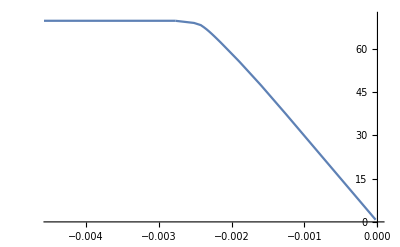

```mathematica
ListLinePlot[listplot]
```

```mathematica
ff[s_]:=1/2(s-nu s)+1/2(s+nu s)Sin[20 Pi/180]- 50 Cos[20 Pi/180]
```

```mathematica
Solve[ff[s]==0,s]
```

{{s→92.162}}

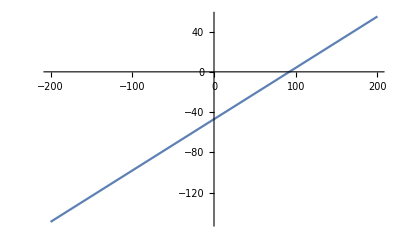

```mathematica
Plot[ff[s],{s,-200,200}]
```

Polygon[{{0,0},{75,0},{75,30},{45,30},{35,40},{0,40}}]

ElementMesh[{{0.,75.},{0.,40.}},{TriangleElement[<945>]}]

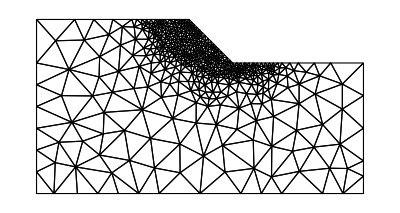

{0.,0.1,0.5,0.7,0.9,0.98,0.99,1.,1.01,1.02,1.03,1.04}

step = 1 lamb = 0. iter = 1 normres = 0.

step = 2 lamb = 0.405 iter = 1 normres = 1192.32

step = 2 lamb = 0.405 iter = 2 normres = 9.3096×10^-10

step = 3 lamb = 2.025 iter = 1 normres = 4769.27

step = 3 lamb = 2.025 iter = 2 normres = 267.727

step = 3 lamb = 2.025 iter = 3 normres = 230.059

step = 3 lamb = 2.025 iter = 4 normres = 100.452

step = 3 lamb = 2.025 iter = 5 normres = 29.6085

step = 3 lamb = 2.025 iter = 6 normres = 7.78925

step = 3 lamb = 2.025 iter = 7 normres = 0.986774

step = 3 lamb = 2.025 iter = 8 normres = 9.72947×10^-6

step = 4 lamb = 2.835 iter = 1 normres = 2384.64

step = 4 lamb = 2.835 iter = 2 normres = 504.944

step = 4 lamb = 2.835 iter = 3 normres = 272.901

step = 4 lamb = 2.835 iter = 4 normres = 220.628

step = 4 lamb = 2.835 iter = 5 normres = 19.9338

step = 4 lamb = 2.835 iter = 6 normres = 3.50216

step = 4 lamb = 2.835 iter = 7 normres = 1.26304

step = 4 lamb = 2.835 iter = 8 normres = 0.000436193

$Aborted

```mathematica
dim=2; (*Problem Dimension*)
order=2; (*Shape functions order*)
thick=1.;(*Thickness*)
globalcounter=1;
young=20000;
nu=0.49;

p=Polygon[{{0,0},{75,0},{75,30},{45,30},{35,40},{0,40}}]
f=Function[{vertices,area},Block[{x,y},{x,y}=Mean[vertices];If[(x-45)^2+(y-49)^2≤22^2,area>0.5,area>10000]]];
m=ToElementMesh[p,MeshRefinementFunction->f,"NodeReordering"->True,"MeshOrder"->order,MaxCellMeasure->25,MeshQualityGoal->"Maximal"]
(*f=Function[{vertices,area},Block[{x,y},{x,y}=Mean[vertices];If[((43<x<46) &&(28<y<31)||(30<x<46) &&(25<y<40)),area>0.01,area>1200]]];
m=ToElementMesh[p,"MeshOrder"->2,MaxCellMeasure->10,MeshRefinementFunction->f]*)
%["Wireframe"]


elastmat={young,nu,20 Pi/180,50};

meshnodes=m["Coordinates"];

topol=m["MeshElements"][[1,1]];

intrule=IntegrationRule[order,dim];

npts=Length[intrule]; 

nglobalpts=Length[topol] npts;

epspvec=Table[0,{nglobalpts},{3}];

epspsolitern=Table[0,{nglobalpts},{3}];

bodyforce={0,-20.}4.05;

coordstofind=Table[{x,0},{x,0,75,0.1}];
idsbottom=DeleteDuplicates[Flatten[Table[FindIds[meshnodes,coordstofind[[i]]],{i,1,Length[coordstofind]}]]];

coordstofind=Table[{0,y},{y,0,45,0.1}];
idsleft=DeleteDuplicates[Flatten[Table[FindIds[meshnodes,coordstofind[[i]]],{i,1,Length[coordstofind]}]]];

coordstofind=Table[{75,y},{y,0,35,0.1}];
idsrigth=DeleteDuplicates[Flatten[Table[FindIds[meshnodes,coordstofind[[i]]],{i,1,Length[coordstofind]}]]];

listplot={};
IterativeProcess[mesh_,fac_]:=Block[{f,fext,meshnodes,lamb,tol=0.00001,print,i,counter,normres,stiff,fint,residual,dw,normu},

globalcounter=1;
meshnodes=mesh["Coordinates"];

f[x_]=0;
fext=ContributeStraigthLineNewman[meshnodes,order,idstop,{0,1},f];


lamb=1./steps;

epspvec=Table[0,{nglobalpts},{3}];

epspsolitern=Table[0,{nglobalpts},{3}];

displace=Table[0,{Length[meshnodes] dim}];

print=True;
counterout=1;
For[i=1,i≤Length[fac],i++,

counter=1;
normres=10;
(*Print["step = ",i];*)
While[counter<10 && normres>tol,
globalcounter=1;
mult=fac[[i]];
{stiff,fint}=Assemble[m,displace];
residual=lamb  fext-fint;
{stiff,residual}=ContributeLineDirichlet[stiff,residual,idsbottom,{1,0}];
{stiff,residual}=ContributeLineDirichlet[stiff,residual,idsbottom,{2,0}];
{stiff,residual}=ContributeLineDirichlet[stiff,residual,idsleft,{1,0}];
{stiff,residual}=ContributeLineDirichlet[stiff,residual,idsrigth,{1,0}];

dw=LinearSolve[stiff,residual,Method->"Banded"];
displace+=dw;
normu=Norm[dw];
normres=Norm[residual];
If[print==True,
Print["step = ",i, " lamb = ",-fac[[i]] bodyforce[[2]]/20,  " iter = ",counter, " normres = ",normres];
];
counter++;
If[normu>10,Break[]];
];
counterout++;
idpostproc=FindIds[meshnodes,{35,40}][[1]];
AppendTo[listplot,{-displace[[idpostproc 2]],-fac[[i]] bodyforce[[2]]/20}];
lamb=counterout/steps//N;
epspsolitern=epspvec;

];
]
fac={0.,0.1,0.5,0.7,0.9,0.98,0.99,1.,1.01,1.02,1.03,1.04}
IterativeProcess[m,fac];
```

InterpolatingFunction[…]

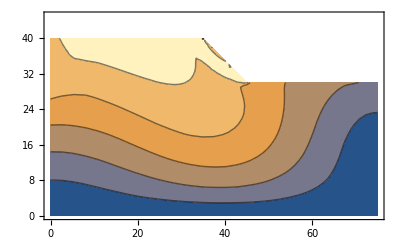

```mathematica
meshnodes=m["Coordinates"];
tab=Flatten[Table[Sqrt[ displace[[i  2]]^2 +displace[[i  2-1]]^2  ],{i, 1,Length[meshnodes] }]];
eufun=ElementMeshInterpolation[{m},tab,"ExtrapolationHandler"->{Function[Indeterminate],"WarningMessage"->False}]
ContourPlot[eufun[x,y],{x,0,75},{y,0,45},AspectRatio->Automatic]
```

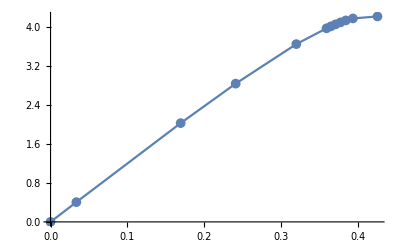

```mathematica
ListLinePlot[listplot,PlotMarkers->{Automatic, 10},PlotRange->All]
```

```mathematica
listplot
```

{{0.,0.},{0.0335958,0.405},{0.169273,2.025},{0.240836,2.835},{0.319698,3.645},{0.359004,3.969},{0.364707,4.0095},{0.370738,4.05},{0.377215,4.0905},{0.384142,4.131},{0.393329,4.1715},{0.425253,4.212}}

```mathematica
ArcTan[0.405/0.0335958]
```

```mathematica
(0.405)/0.0335958
```

12.0551

Polygon[{{0,0},{75,0},{75,30},{45,30},{45,40},{0,40}}]

ElementMesh[{{0.,75.},{0.,40.}},{TriangleElement[<1162>]}]

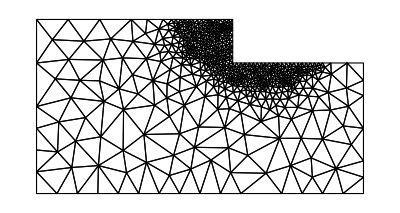

{0.4,0.8,0.94,0.96,0.98,0.99,0.995,0.999}

step = 1 lamb = 0.4 iter = 1 normres = 1124.7

step = 1 lamb = 0.4 iter = 2 normres = 31.5054

step = 1 lamb = 0.4 iter = 3 normres = 3.75512

step = 1 lamb = 0.4 iter = 4 normres = 0.205514

step = 1 lamb = 0.4 iter = 5 normres = 0.0000113151

step = 1 lamb = 0.4 iter = 6 normres = 1.57548×10^-10

step = 2 lamb = 0.8 iter = 1 normres = 1124.7

step = 2 lamb = 0.8 iter = 2 normres = 106.078

step = 2 lamb = 0.8 iter = 3 normres = 62.0502

step = 2 lamb = 0.8 iter = 4 normres = 8.63897

step = 2 lamb = 0.8 iter = 5 normres = 1.54734

step = 2 lamb = 0.8 iter = 6 normres = 0.014027

step = 2 lamb = 0.8 iter = 7 normres = 7.66245×10^-7

step = 3 lamb = 0.94 iter = 1 normres = 393.646

step = 3 lamb = 0.94 iter = 2 normres = 68.7751

step = 3 lamb = 0.94 iter = 3 normres = 42.7116

step = 3 lamb = 0.94 iter = 4 normres = 13.3758

step = 3 lamb = 0.94 iter = 5 normres = 3.95221

step = 3 lamb = 0.94 iter = 6 normres = 0.274019

step = 3 lamb = 0.94 iter = 7 normres = 0.000221804

step = 3 lamb = 0.94 iter = 8 normres = 5.33977×10^-10

step = 4 lamb = 0.96 iter = 1 normres = 56.2351

step = 4 lamb = 0.96 iter = 2 normres = 18.4433

step = 4 lamb = 0.96 iter = 3 normres = 7.83682

step = 4 lamb = 0.96 iter = 4 normres = 0.811932

step = 4 lamb = 0.96 iter = 5 normres = 0.0287641

step = 4 lamb = 0.96 iter = 6 normres = 0.0000467389

step = 4 lamb = 0.96 iter = 7 normres = 4.45422×10^-10

step = 5 lamb = 0.98 iter = 1 normres = 56.2351

step = 5 lamb = 0.98 iter = 2 normres = 19.115

step = 5 lamb = 0.98 iter = 3 normres = 17.559

step = 5 lamb = 0.98 iter = 4 normres = 23.3168

step = 5 lamb = 0.98 iter = 5 normres = 20.5087

step = 5 lamb = 0.98 iter = 6 normres = 20.4914

step = 5 lamb = 0.98 iter = 7 normres = 11.7412

step = 5 lamb = 0.98 iter = 8 normres = 6.07269

step = 5 lamb = 0.98 iter = 9 normres = 2.66142

step = 6 lamb = 0.99 iter = 1 normres = 29.0062

step = 7 lamb = 0.995 iter = 1 normres = 533.614

step = 8 lamb = 0.999 iter = 1 normres = 1.74357×10^8

```mathematica
dim=2; (*Problem Dimension*)
order=2; (*Shape functions order*)
thick=1.;(*Thickness*)
globalcounter=1;
young=20000;
nu=0.49;

p=Polygon[{{0,0},{75,0},{75,30},{45,30},{45,40},{0,40}}]
f=Function[{vertices,area},Block[{x,y},{x,y}=Mean[vertices];If[(x-52)^2+(y-47)^2≤22^2,area>0.5,area>10000]]];
m=ToElementMesh[p,MeshRefinementFunction->f,"NodeReordering"->True,"MeshOrder"->order,MaxCellMeasure->25,MeshQualityGoal->"Maximal"]
(*f=Function[{vertices,area},Block[{x,y},{x,y}=Mean[vertices];If[((43<x<46) &&(28<y<31)||(30<x<46) &&(25<y<40)),area>0.01,area>1200]]];
m=ToElementMesh[p,"MeshOrder"->2,MaxCellMeasure->10,MeshRefinementFunction->f]*)
%["Wireframe"]


elastmat={young,nu,0.00001 Pi/180,50};

meshnodes=m["Coordinates"];

topol=m["MeshElements"][[1,1]];

intrule=IntegrationRule[order,dim];

npts=Length[intrule]; 

nglobalpts=Length[topol] npts;

epspvec=Table[0,{nglobalpts},{3}];

epspsolitern=Table[0,{nglobalpts},{3}];

bodyforce={0,-20.};

coordstofind=Table[{x,0},{x,0,75,0.1}];
idsbottom=DeleteDuplicates[Flatten[Table[FindIds[meshnodes,coordstofind[[i]]],{i,1,Length[coordstofind]}]]];

coordstofind=Table[{0,y},{y,0,45,0.1}];
idsleft=DeleteDuplicates[Flatten[Table[FindIds[meshnodes,coordstofind[[i]]],{i,1,Length[coordstofind]}]]];

coordstofind=Table[{75,y},{y,0,35,0.1}];
idsrigth=DeleteDuplicates[Flatten[Table[FindIds[meshnodes,coordstofind[[i]]],{i,1,Length[coordstofind]}]]];

listplot={};
IterativeProcess[mesh_,fac_]:=Block[{f,fext,meshnodes,lamb,tol=0.00001,print,i,counter,normres,stiff,fint,residual,dw,normu},

globalcounter=1;
meshnodes=mesh["Coordinates"];

f[x_]=0;
fext=ContributeStraigthLineNewman[meshnodes,order,idstop,{0,1},f];


lamb=1./steps;

epspvec=Table[0,{nglobalpts},{3}];

epspsolitern=Table[0,{nglobalpts},{3}];

displace=Table[0,{Length[meshnodes] dim}];

print=True;
counterout=1;
For[i=1,i≤Length[fac],i++,

counter=1;
normres=10;
(*Print["step = ",i];*)
While[counter<10 && normres>tol,
globalcounter=1;
mult=fac[[i]];
{stiff,fint}=Assemble[m,displace];
residual=lamb  fext-fint;
{stiff,residual}=ContributeLineDirichlet[stiff,residual,idsbottom,{1,0}];
{stiff,residual}=ContributeLineDirichlet[stiff,residual,idsbottom,{2,0}];
{stiff,residual}=ContributeLineDirichlet[stiff,residual,idsleft,{1,0}];
{stiff,residual}=ContributeLineDirichlet[stiff,residual,idsrigth,{1,0}];

dw=LinearSolve[stiff,residual,Method->"Banded"];
displace+=dw;
normu=Norm[dw];
normres=Norm[residual];
If[print==True,
Print["step = ",i, " lamb = ",-fac[[i]] bodyforce[[2]]/20,  " iter = ",counter, " normres = ",normres];
];
counter++;
If[normu>10,Break[]];
];
counterout++;
idpostproc=FindIds[meshnodes,{45,40}][[1]];
AppendTo[listplot,{-displace[[idpostproc 2]],-fac[[i]] bodyforce[[2]]/20}];
lamb=counterout/steps//N;
epspsolitern=epspvec;

];
]
fac={  0.4, 0.8, 0.94,0.95,0.96,0.97,0.98,0.985,0.99}
IterativeProcess[m,fac];
```

```mathematica
listplot
```

{{0.0299237,0.4},{0.0772131,0.8},{0.114081,0.94},{0.123133,0.96},{0.49885,0.98},{3.79107,0.99},{206.194,0.995},{340948.,0.999}}

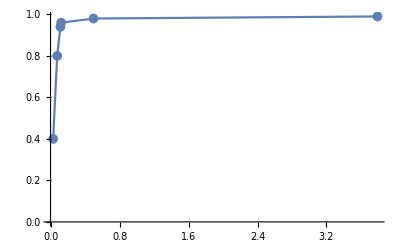

```mathematica
ListLinePlot[{{0.02992368547098801,0.4},{0.0772130576478246,0.8},{0.11408059353736956,0.94},{0.12313285262961168,0.96},{0.49885006510412333,0.98},{3.7910660024201914,0.99}},PlotMarkers->{Automatic, 10},PlotRange->All]
```